## Para un n fija

## Definiciones

```mathematica
h=4.135667696*10^(-15); (*eV s*)
ℏ=6.582119569*10^(-16); (*eV s*)
c=3*^17 ;(*nm s^-1*)
Res=1*10^(-8);
```

## Definiciones

```mathematica
h=4.135667696*10^(-15); (*eV s*)
ℏ=6.582119569*10^(-16); (*eV s*)
c=3*^17 ;(*nm s^-1*)
```

### Datos experimentales

```mathematica
ψn[n_,ρ_]:= ρ*SphericalBesselJ[n,ρ]
```

```mathematica
ξn[n_,ρ_]:=ρ*SphericalHankelH1[n,ρ]
```

```mathematica
dψn[n_,ρ_]:=-n *SphericalBesselJ[n,ρ]+ ρ * SphericalBesselJ[n-1,ρ] 
dξn[n_,ρ_]:=-n * SphericalHankelH1[n,ρ] + ρ* SphericalHankelH1[n-1,ρ]
```

```mathematica
mieCoefAn[np_,nm_,a_,λ_,n_]:=Module[{m,x,an},
						m=np/nm;
						x=(2 Pi nm a)/λ;							
						an=((m ψn[n,m x] dψn[n,x])-(ψn[n,x] dψn[n,m x]))/((m ψn[n,m x] dξn[n,x])-(ξn[n,x] dψn[n,m x])); 
						an]
```

```mathematica
mieCoefBn[np_,nm_,a_,λ_,n_]:=Module[{m,x,bn},
						m=np/nm;
						x=(2 Pi nm a)/λ;							
						bn=((ψn[n,m x] dψn[n,x])-(m ψn[n,x] dψn[n,m x]))/((ψn[n,m x] dξn[n,x])-(m ξn[n,x] dψn[n,m x]));
						bn]
```

## Modelo de Drude

```mathematica
ϵ[λ_,λp_,γ_]:=1-((2 Pi c/λp)^2/((2 Pi c/λ)((2 Pi c/λ)+ I γ)))(*recibe λ en nm*)
```

```mathematica
ϵmieCoefAn[nm_,a_,λ_,n_,λp_,γ_]:=Module[{np,m,x,an},
						np=Sqrt[1-((2 Pi c/λp)^2/((2 Pi c/λ)((2 Pi c/λ)+ I γ)))];
						m=np/nm;
						x=(2 Pi nm a)/λ;							
						an=((m ψn[n,m x] dψn[n,x])-(ψn[n,x] dψn[n,m x]))/((m ψn[n,m x] dξn[n,x])-(ξn[n,x] dψn[n,m x])); 
						an]
```

```mathematica
ϵmieCoefBn[nm_,a_,λ_,n_,λp_,γ_]:=Module[{np,m,x,bn},
						np=Sqrt[1-((2 Pi c/λp)^2/((2 Pi c/λ)((2 Pi c/λ)+ I γ)))];
						m=np/nm;
						x=(2 Pi nm a)/λ;							
						bn=((ψn[n,m x] dψn[n,x])-(m ψn[n,x] dψn[n,m x]))/((ψn[n,m x] dξn[n,x])-(m ξn[n,x] dψn[n,m x]));
						bn]
```

### Datos experimentales

```mathematica
nmieQsca[np_,nm_,a_,λ_,n_]:=Module[{an,bn,k,Csca,Qsca},
an=mieCoefAn[np,nm,a,λ,n];
bn=mieCoefBn[np,nm,a,λ,n];
Csca= (λ^2 )/(2*π* Norm[nm]^2)*((2 n +1)(Norm[an]^2+Norm[bn] ^2));
Qsca=Csca/(Pi* a^2) ;
{an,bn,Csca,Qsca}]
```

```mathematica
nmieQext[np_,nm_,a_,λ_,n_]:=Module[{an,bn,Cext,Qext},
an=mieCoefAn[np,nm,a,λ,n];
bn=mieCoefBn[np,nm,a,λ,n];
Cext =(λ^2 )/(2*π* Norm[nm]^2)* ((2 n +1)Re[an + bn]);
Qext=Cext/(Pi* a^2) ;{an,bn,Cext,Qext}]
```

### Modelo de Drude

```mathematica
nϵmieQsca[nm_,a_,λ_,n_,λp_,γ_]:=Module[{an,bn,k,Csca,Qsca},
an=ϵmieCoefAn[nm,a,λ,n,λp,γ];
bn=ϵmieCoefBn[nm,a,λ,n,λp,γ];
Csca= (λ^2 )/(2*π* Norm[nm]^2)*((2 n +1)(Norm[an]^2+Norm[bn] ^2));

Qsca=Csca/(Pi* a^2) ;
{an,bn,Csca,Qsca}]
```

```mathematica
nϵmieQext[nm_,a_,λ_,n_,λp_,γ_]:=Module[{an,bn,Cext,Qext},
an=ϵmieCoefAn[nm,a,λ,n,λp,γ];
bn=ϵmieCoefBn[nm,a,λ,n,λp,γ];
Cext =(λ^2 )/(2*π* Norm[nm]^2)*((2 n +1)Re[an+ bn]);
Qext=Cext/(Pi* a^2) ;
{an,bn,Cext,Qext}]
```

## Cálculos

### Modelo de Drude

#### Para ℏω = 13.142 eV, ℏγ = 0.197 eV y a = 60 nm

```mathematica
result1=Table[{λ,nϵmieQext[1,#,λ,1,2 Pi c/(13.142/ℏ),0.197/ℏ][[4]]},{λ,50,450}]&/@{5,10,20,30,40,50};
```

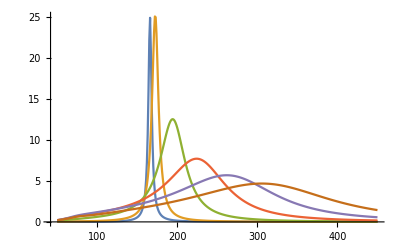

```mathematica
ListLinePlot[result1,AxesLabel->{"",""},PlotRange->All]
```

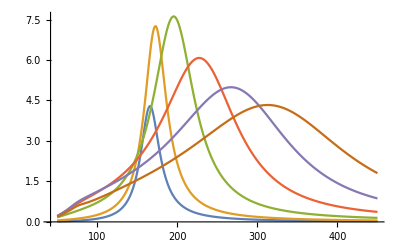

```mathematica
result2=Table[{λ,nϵmieQext[1,#,λ,1,2 Pi c/(13.142/ℏ),(13.142/ℏ)*0.1][[4]]},{λ,50,450}]&/@{5,10,20,30,40,50};
ListLinePlot[result2,AxesLabel->{"",""},PlotRange->All]
```

```mathematica
GoldenSearchMax[f_,lower_,upper_]:=Module[{a=N[lower],b=N[upper],c,d},k=0;
While[Abs[(b-(b-a)/GoldenRatio)-(a+(b-a)/GoldenRatio)]>Res,c=(b-(b-a)/GoldenRatio);
d=(a+(b-a)/GoldenRatio);
If[f[c]>f[d],(*Then*)b=d(*Else*); k=k+1;,a=c;k++;]];Return[(b+a)/2]];
```

```mathematica
L1[λ_]:=nϵmieQext[1,0.001,λ,1,2 Pi c/(13.142/ℏ),0.197/ℏ][[6]]
L2[λ_]:=nϵmieQext[1,1,λ,2,2 Pi c/(13.142/ℏ),0.197/ℏ][[6]]
L3[λ_]:=nϵmieQext[1,1,λ,2,2 Pi c/(13.142/ℏ),0.197/ℏ][[6]]
```

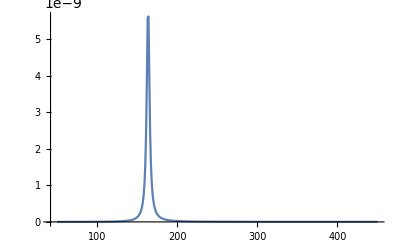

```mathematica
ListLinePlot[Table[{λ,nϵmieQext[1,1*10 ^(-9),λ,1,2 Pi c/(13.142/ℏ),0.197/ℏ][[6]]},{λ,50,450}],PlotRange->All]
```

```mathematica
s=GoldenSearchMax[L1,50,450]
```

163.518

```mathematica
(2 Pi c/(13.142/ℏ))/163.51818424461214
```

0.57735

```mathematica
ωl[ωp_,l_]:=Sqrt[l/(2 l +1)]
```

```mathematica
N[ωl[2 Pi c/(13.142/ℏ),1]]
```

0.57735

```mathematica
s=ConstantArray[0,10]
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
For[a=1,a<=10,a++,L1[λ_]:=nϵmieQext[1,a,λ,1,2 Pi c/(13.142/ℏ),0.197/ℏ][[6]];s[[a]]=GoldenSearchMax[L1,50,450]]
```

```mathematica
s
```

{163.615,163.903,164.381,165.043,165.883,166.893,168.064,169.387,170.852,172.451}

```mathematica
lst={163.61471356941666,163.90337140490436,164.38118975752718,165.0432700637793,165.88307063921405,166.89276839604042,168.0636504473655,169.38650095435935,170.85195836480648,172.45082223410617}
```

{163.615,163.903,164.381,165.043,165.883,166.893,168.064,169.387,170.852,172.451}

```mathematica
Style["Algo", FontFamily->"Algerian", FontSize->24]
```

Algo